```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
(1) we solve numerically the background (inflaton , Hubble ),the daughter mode function  and number density  for different  modes. In the spectator dynamics , we neglet the contribution from universe's expansion.
(2) we plot the Power spectrum of the daughter field and the number density of the daughter specie.
(3) Finally, we compute the GW generation due to daughter energy stress tensor. *)
```

# Preheating scenario

```mathematica
Mpl=1.0;                    (* reduced mass Planck *)
mϕ=1.0*Mpl;           (* inflation mass *)
λ = 1.0;                       (* self-coupling constant *)
g=200.0;                    (* coupling constant ϕ-χ *)
tMax=50.0;               (* time *)
Φ0=0.1 Mpl;                (* initial amplitude ϕ *)
```

## Solving Background dynamic

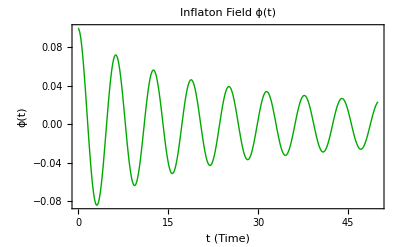

```mathematica
(* Background equations: EOM Inflaton field, Friedman equation *)
H[ϕ_,dϕ_]:=√(1/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2+ λ/4 ϕ^4));
eqa = a'[t]==a[t]*H[ϕ[t],ϕ'[t]];
eqϕ=ϕ''[t]+3H[ϕ[t],ϕ'[t]]ϕ'[t]+mϕ^2 ϕ[t]+λ ϕ[t]^3==0;

(*Initial conditions*)
backgroundconditions = {a[0]==1,ϕ[0]==Φ0,ϕ'[0]==0};

(* Solve Background dynamic *)
solbackground=NDSolve[{eqϕ,eqa,backgroundconditions[[1]],backgroundconditions[[2]],backgroundconditions[[3]]},{ϕ,a},{t,0,tMax},Method->"StiffnessSwitching",MaxSteps->Infinity];

(* Solution's background *)
ϕsol[t_]:=Evaluate[ϕ[t]/. solbackground[[1]]];
asol[t_]:=Evaluate[a[t]/. solbackground[[1]]];
Hsol[t_]:=H[ϕsol[t],ϕsol'[t]];

ϕPlot = Plot[ϕsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Darker[Green]},Frame->True,FrameLabel->{"t (Time)","ϕ(t)"},PlotLabel->"Inflaton Field ϕ(t)"]
```

## Daughter dynamic

```mathematica
(* Frequency *)
ω2[t_,k_]:=k^2+g^2 ϕsol[t]^2;
ω[t_,k_]:=√ω2[t,k];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t,k]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0,k])),χ'[0]==-I*√(ω[0,k]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=ParametricNDSolveValue[{eqχ,χconditions[[1]],χconditions[[2]]},χ,{t,0,tMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching",MaxSteps->Infinity];

(* Daughter solution *)
χsol[k_,t_]:=solχ[k][t];

(* Number density particles *)
numberχ[t_,k_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[t]]^2/ω[t,k]+ω[t,k]/2 Abs[χsolK[t]]^2-1/2
];
```

## Evaluate for specific momenta

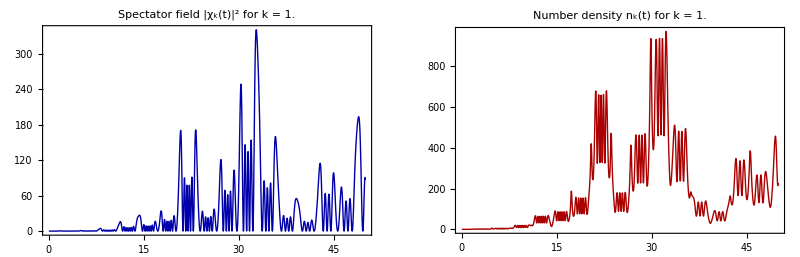

```mathematica
kexample = 1.0;
χPlot = Plot[Abs[χsol[kexample,t]]^2,{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Darker[Blue]},Frame->True,PlotLabel->Style[StringForm["Spectator field |χ_k(t)|^2 for k = ``",kexample]]];
nχPlot = Plot[numberχ[t,kexample],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Darker[Red]},Frame->True,PlotLabel->Style[StringForm["Number density n_k(t) for k = ``",kexample]]];
GraphicsGrid[Partition[{χPlot,nχPlot},2,2,{1,2},""]]
```

## Resonance parameter

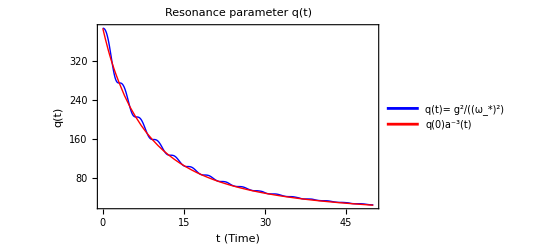

(Broad resonance regime) Maximum resonance parameter: 388.35

Parametric resonance up to k_* = q^(1/4) = 4.43921

```mathematica
ωstar[Φ_,t_]:=√(mϕ^2+ 3λ Φ[t]^2);
Φ[t_]:=√(ϕsol[t]^2 + (ϕsol'[t])^2/ωstar[ϕsol,t]^2);
q[t_]:=(g^2 Φ[t]^2)/ωstar[Φ,t]^2; (* definition *)
Plot[{q[t],q[0]*asol[t]^-3},{t,0,tMax},PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,FrameLabel->{"t (Time)","q(t)"},PlotLegends->{"q(t)= g^2/(ω_*)^2","q(0)a^-3(t)"},PlotLabel->"Resonance parameter q(t)"]
If[q[0]>1,Print["\n (Broad resonance regime) Maximum resonance parameter: ",q[0]],Print["\n (Narrow resonance regime) Maximum resonance parameter: ",q[0]]];
Print["\n Parametric resonance up to k_* = q^(1/4) = ",q[0]^(1/4)]
```

## Power spectrum of the Daughter field

```mathematica
PSχ[k_,τ_]:=k^3/(2 π^2)  Abs[χsol[k,τ]]^2 ;

χSpectrum[kList_List,τ_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχ[k,τ]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];

nχSpectrum[kList_List,τ_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,numberχ[τ,k]},{k,kList}],Row[{"Computation nχ for k = ",currentK}]]
];
```

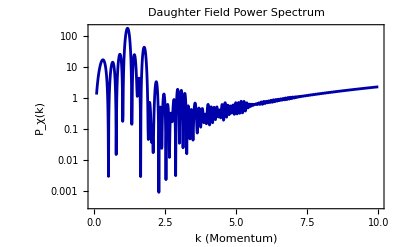

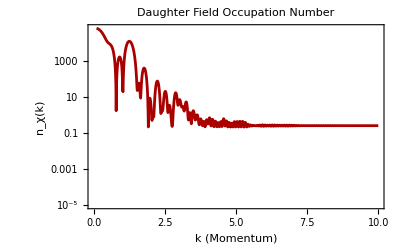

```mathematica
(* Range values *)
kValsχ=Range[0.1,10.0,0.01];

spectrumχ=χSpectrum[kValsχ,tMax];
spectrumnχ=nχSpectrum[kValsχ,tMax];

(* Plot *)
plotSpectrumχ=ListLogPlot[spectrumχ,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"k (Momentum)","P_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Blue]},GridLines->Automatic,PlotLabel->"Daughter Field Power Spectrum"]

plotSpectrumnχ=ListLogPlot[spectrumnχ,Joined->True,PlotRange->{{0,10},{10^-5,Automatic}},Frame->True,FrameLabel->{"k (Momentum)","n_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Red]},GridLines->Automatic,PlotLabel->"Daughter Field Occupation Number"]
```

# GW

## Compute the Power spectrum of GWs

```mathematica
(*  ,  *)
TimeIntegral[k_,p_,x_,τ_]:=Module[{kp,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];

Quiet[
Ic=NIntegrate[Cos[k*t]*χsol[p,t]*χsol[kp,t],{t,0,τ},Method->"LevinRule",MaxRecursion->30,AccuracyGoal->4,PrecisionGoal->4];
Is=NIntegrate[Sin[k*t]*χsol[p,t]*χsol[kp,t],{t,0,τ},Method->"LevinRule",MaxRecursion->30,AccuracyGoal->4,PrecisionGoal->4];{NIntegrate::slwcon,NIntegrate::ncvb}];

(*  *)
(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];

(*  *)
GWGrid[k_,τ_,pMax_:100,dp_:2,dx_:0.1]:=Module[{grid},
grid=Flatten[ParallelTable[{{p,x},TimeIntegral[k,p,x,τ]},{p,0.001,pMax,dp},{x,-1.0,1.0,dx}],1];
grid
];

funzρGWO[k_,τ_,pMax_:100,dp_:2,dx_:0.1]:=Module[{gridData,interpFunc,res},
gridData=GWGrid[k,τ,pMax,dp,dx];
interpFunc=Interpolation[gridData,InterpolationOrder->2];

(* integrate *)
res=NIntegrate[interpFunc[p,x],{p,0.001,pMax},{x,-1,1},Method->"GlobalAdaptive"];
k^3/(2 π^3) *res
];

GWSpectrum[kList_List,τ_,pMax_:100,dp_:2,dx_:0.1]:=Module[{currentK},

Monitor[Table[currentK=k;{k,funzρGWO[k,τ,pMax,dp,dx]},{k,kList}],Row[{"Calculating spectrum... currently evaluating k = ",currentK}]]
];
```

## Power spectrum

```mathematica
kValsGW={1.,3.,5.,8.};

(*
kValsGW=Join[Range[0.1,1.0,0.1],(*IR tail:0.1 to 1.0*)
Range[1.2,6.0,0.2],(*Main peak region:fine resolution*)
Range[6.2,10.0,0.5]   (*UV tail:out to 15 to see it drop off*)
];

kValsGW=Join[Range[0.1,1.0,0.1],(*Captures the low-k IR tail*)
Range[1.2,4.5,0.2],(*High resolution over the peak*)
Range[4.25,6.0,0.25]  (*Captures the UV drop-off past k_max*)];

kValsGW=Join[Range[0.1,1.0,0.2],(*IR Tail*)
Range[1.5,8.5,0.5],(*The broad GW plateau/peak sourced by pairs*)
Range[9.0,12.0,0.5]   (*The true UV drop-off past 2*p_max*)];
*)
spectrumGW=GWSpectrum[kValsGW,tMax];
```

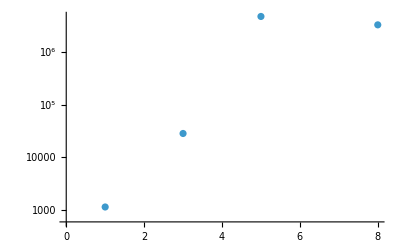

```mathematica
ListLogPlot[spectrumGW]
```

## Save data

```mathematica
(* Power spectrum χ *)
fileNameχCSV="DaughterSpectrumPreheating.csv";
fileNamenχCSV="DaughterNumberParticleSpectrumPreheating.csv";
fileNameGWCSV="GWSpectrumPreheating.csv";

Print["Saving data to: ",NotebookDirectory[],"\\",fileNameχCSV];
Export[fileNameχCSV,spectrumχ];
Print["Saving data to: ",NotebookDirectory[],"\\",fileNamenχCSV];
Export[fileNamenχCSV,spectrumnχ];
Print["Saving data to: ",NotebookDirectory[],"\\",fileNameGWCSV];
Export[fileNameGWCSV,spectrumGW];
```

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\DaughterSpectrumPreheating.csv

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\DaughterNumberParticleSpectrumPreheating.csv

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\GWSpectrumPreheating.csv

```mathematica
(* Import the saved data
savedSpectrumχ = Import["DaughterSpectrumPreheating.csv"];
savedSpectrumnχ = Import["DaughterNumberParticleSpectrumPreheating.csv"];
savedSpectrumGW = Import["GWSpectrumPreheating.csv"]*)
```